```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Error while cosntraining u *)
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,maxError_]:=
Module[{InitGuess,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = {0,0,0,0};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];


froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
While[error > maxError,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[τ - t], xdot -> xdot1a[τ - t], θ ->θ1a[τ - t], θdot -> θdot1a[τ - t], u -> u1a[τ - t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,S,K},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
ufb[t_] := Piecewise[{{
K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

Now we choose a large enough n and vary the time horizon to understand the behaviour of u. Fix an initial condition

```mathematica
PlotFF[n_,τ_,A_,order_,maxIter_,maxError_,ICs_] := Module[{τ1,plot,x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0},
τ1 = 1.25*τ;
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError]]; plot=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->StringJoin["τ = ",ToString[τ]] ,AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
plot]
```

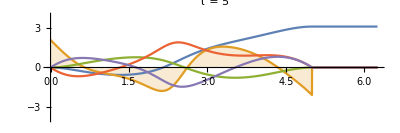
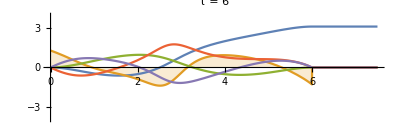
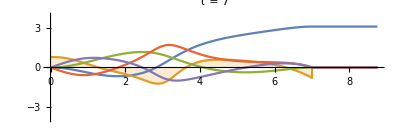
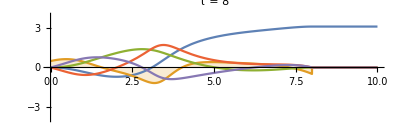
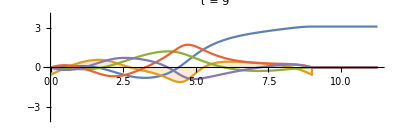
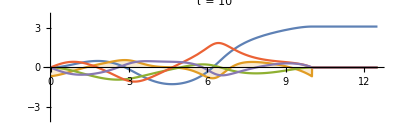
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
n=60;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 30;maxError = 0.01;
ICs = {0,0,0,0};
τStart = 5; τEnd = 10; τStep = 1;numberPlots = IntegerPart[(τEnd - τStart) / (τStep)]+1;
plots = Table[PlotFF[n,τ,A,order,maxIter,maxError,ICs],{τ,τStart,τEnd,τStep}];
Grid[Join[Table[Table[plots[[i]],{i,j,j+2}],{j,1,3*IntegerPart[numberPlots/3],3}],Table[Table[plots[[i]],{i,3*IntegerPart[numberPlots/3]+1,numberPlots}],{j,1,1}]]]
```

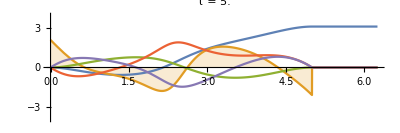
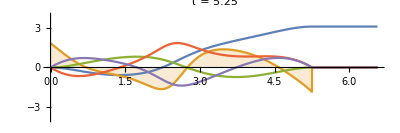
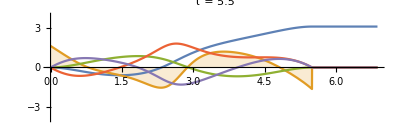
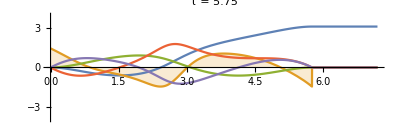
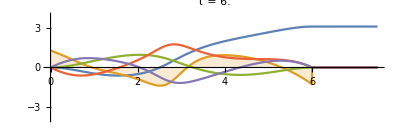
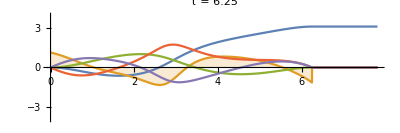
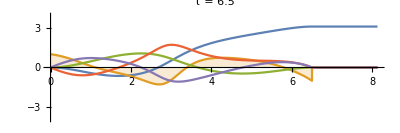
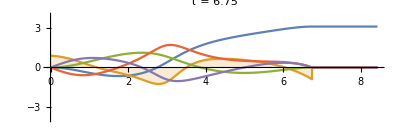
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
n=60;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 30;maxError = 0.01;
ICs = {0,0,0,0};
τStart = 5; τEnd = 10; τStep = 0.25;numberPlots = IntegerPart[(τEnd - τStart) / (τStep)]+1;
plots = Table[PlotFF[n,τ,A,order,maxIter,maxError,ICs],{τ,τStart,τEnd,τStep}];
Grid[Join[Table[Table[plots[[i]],{i,j,j+2}],{j,1,3*IntegerPart[numberPlots/3],3}],Table[Table[plots[[i]],{i,3*IntegerPart[numberPlots/3]+1,numberPlots}],{j,1,1}]]]
```

## “Swing Up Pendulum” Two Point Boundary Value Problem Formulation

Implement Feedforward Calculations

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
ffCalc[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff,θdotff,uff,λff,λdotff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}]:={θdot,-Sin[θ]-λ,λdot,λ (-Cos[θ])};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}==1/2 Δt (f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])+{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
froot=FindRoot[eqns,sv];
θff=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ}];
θdotff=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ}];
λff = ListInterpolation[Table[Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];
λdotff = ListInterpolation[Table[Subscript[λdot, i],{i,0,n}]/.froot,{0,τ}];
uff=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];
{θff,θdotff,uff,λff,λdotff}
]
ffCalcDiscrete[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff,θdotff,uff,λff,λdotff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}]:={θdot,-Sin[θ]-λ,λdot,λ (-Cos[θ])};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}==1/2 Δt (f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])+{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
froot=FindRoot[eqns,sv];
θff=Table[Subscript[θ, i],{i,0,n}]/.froot;
θdotff=Table[Subscript[θdot, i],{i,0,n}]/.froot;
λff = Table[Subscript[λ, i],{i,0,n}]/.froot;
λdotff = Table[Subscript[λdot, i],{i,0,n}]/.froot;
uff=Table[-Subscript[λ, i],{i,0,n}]/.froot;
{θff,θdotff,uff,λff,λdotff}
]
```

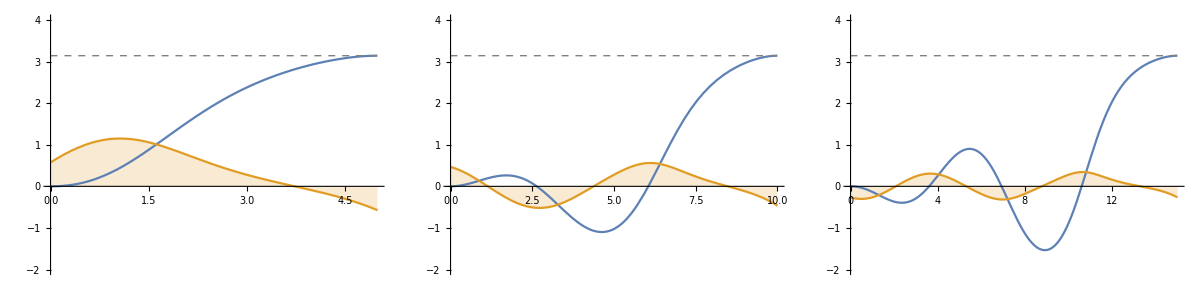

```mathematica
n=200;  
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,5];
{θ2,θdot2,u2,λ2,λdot2}=ffCalc[n,10];
{θ3,θdot3,u3,λ3,λdot3}=ffCalc[n,15];
p1=Plot[{θ1[t],u1[t],π},{t,0,5},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
p2=Plot[{θ2[t],u2[t],π},{t,0,10},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
p3=Plot[{θ3[t],u3[t],π},{t,0,15},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];

Grid[{{p1,p2,p3}},Spacings->5]
```

Implement End Point Map and Compute the Jacobian of the Shooting Function

```mathematica
EndPointMap[f_,xBase_,xPerturb_,xsym_,nDim_,T_] := Module[{fGrad,x,t,eq,init},
fGrad = Grad[f,xsym]; (* f has to be a function of x*)
eq={x'[t] == Flatten[(fGrad/.{Table[xsym[[i]] -> xBase[[i]][t],{i,1,nDim}]}),1].x[t]};
init = {x[0] == xPerturb};
x=NDSolveValue[{eq,init},x,{t,0,T},Method->{"DiscontinuityProcessing"->None}];
x[T]]
```

Test End Point Map

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=20; 
xPerturb = {0.001,0.001,0.001,0.001};
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
EndPointMap[f,xBase,xPerturb,xsym,nDim,T]
```

{-0.028419,-0.0293697,0.00238627,0.00230536}

Compute the Jacobian of the Shooting Function

```mathematica
ComputeJacobian[f_,xBase_,xsym_,nDim_,T_] := Module[{J,e1,e2,e3,e4,f1,f2,f3,f4,M1},
e1 = {1,0,0,0};
e2 = {0,1,0,0};
e3 = {0,0,1,0};
e4 = {0,0,0,1};
f1 = EndPointMap[f,xBase,e1,xsym,nDim,T];
f2 = EndPointMap[f,xBase,e2,xsym,nDim,T];
f3 = EndPointMap[f,xBase,e3,xsym,nDim,T];
f4 = EndPointMap[f,xBase,e4,xsym,nDim,T];
M1 = {f1,f2,f3,f4}ᵀ;
(* For this specific Case of Shooting Function, the Jacobian will be the Top Right part of the Entire jacobian *)
J = M1[[1;;nDim/2,nDim/2+1;;nDim]]
]
ComputeJacobianEntire[f_,xBase_,xsym_,nDim_,T_] := Module[{J,e1,e2,e3,e4,f1,f2,f3,f4,M1},
e1 = {1,0,0,0};
e2 = {0,1,0,0};
e3 = {0,0,1,0};
e4 = {0,0,0,1};
f1 = EndPointMap[f,xBase,e1,xsym,nDim,T];
f2 = EndPointMap[f,xBase,e2,xsym,nDim,T];
f3 = EndPointMap[f,xBase,e3,xsym,nDim,T];
f4 = EndPointMap[f,xBase,e4,xsym,nDim,T];
M1 = {f1,f2,f3,f4}ᵀ;
(* For this specific Case of Shooting Function, the Jacobian will be the Top Right part of the Entire jacobian *)
J = M1
]
```

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=20; 
xPerturb = {0.001,0.001,0.001,0.001};
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
ComputeJacobian[f,xBase,xsym,nDim,T]
```

{{0.756218,0.771165},{-12.1236,-12.0127}}

Test the Jacobian by Recomputing the solution from scratch

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; 
xPerturb = {0.001,0.001};
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
J =ComputeJacobian[f,xBase,xsym,nDim,T];
xFinal3 = Table[EndPointMap[f,xBase,Join[{0,0},xPerturb],xsym,nDim,T][[i]],{i,1,2}]+ {θ1[T],θdot1[T]}
xFinal = J.xPerturb + {θ1[T],θdot1[T]}

eq={θ'[t] == θdot[t],θdot'[t] == -Sin[θ[t]]-λ[t],λ'[t] == λdot[t],λdot'[t] == λ[t] *(-Cos[θ[t]])};
init = {θ[0] == 0,θdot[0] == 0,λ[0] == λ1[0] + xPerturb[[1]],λdot[0] == λdot1[0]+xPerturb[[2]]};
{θs,θdots,λs,λdots}=NDSolveValue[{eq,init},{θ,θdot,λ,λdot},{t,0,T},Method->{"DiscontinuityProcessing"->None}];
xFinal2 = {θs[T],θdots[T]}
```

{3.10032,-0.0479016}

{3.10032,-0.0479009}

{3.10013,-0.0479837}

Update Functions used in the Algorithm

```mathematica
UpdateJacobianTime[J_,dT_,f_,xsym_,nDim_] := Module[{e,F,fGrad},
(*Will have to pass the entire Jacobian and not that of the shooting function  *)
fGrad = Grad[f,xsym]; (* f has to be a function of x*)
e = Table[J[[;;,i]],{i,1,nDim}];
F = Table[e[[j]] + dT*(Flatten[fGrad/.{Table[xsym[[i]] -> e[[j]][[i]],{i,1,nDim}]},1]).e[[j]],{j,1,nDim}];
Fᵀ]
```

```mathematica
UpdateEndState[xEnd_,f_,xsym_,T_,dT_,nDim_] := Module[{xNew},
xNew = Table[xEnd[[i]] + dT*(f/.(Table[xsym[[j]]->xEnd[[j]],{j,1,nDim}]))[[i]],{i,1,nDim}]
]
```

```mathematica
UpdateInitialState[λOld_,JShooting_,xEnd_,xStar_] := Module[{λNew},
λNew = λOld - Inverse[JShooting].(xEnd - xStar)
]
```

```mathematica
CorrectEndState[xEndOld_,λEndOld_,JEntire_,λInitOld_,λInitNew_,nDim_] :=Join[xEndOld,λEndOld] + JEntire.(Join[Table[0,{i,1,nDim/2}],λInitNew - λInitOld]);
```

Test Update Jacobian and Update base Time

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.001;
xPerturb = {0.001,0.001};
{θ1,θdot1,u1,λ1,λdot1}=ffCalcDiscrete[n,T];
xBaseDiscrete = {θ1,θdot1,λ1,λdot1};
xEnd = Table[Last[xBaseDiscrete[[i]]],{i,1,nDim}];
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
xNew  = UpdateEndState[xEnd,f,xsym,T,dT,nDim];
```

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.001;
xPerturb = {0.001,0.001};
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
J1 =ComputeJacobianEntire[f,xBase,xsym,nDim,T];
J2 = ComputeJacobianEntire[f,xBase,xsym,nDim,T+dT];
J3 = UpdateJacobianTime[J1,dT,f,xsym,nDim];
```

Test UpdateInitialState

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.001;
{θ1,θdot1,u1,λ1,λdot1}=ffCalcDiscrete[n,T];
xBaseDiscrete = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
xNew  = UpdateEndState[xBaseDiscrete,f,xsym,T,dT,nDim];
{θ2,θdot2,u2,λ2,λdot2}=ffCalcDiscrete[n,T+dT];
JEntire = UpdateJacobianTime[J1,dT,f,xsym,nDim];
JShooting = JEntire[[1;;nDim/2,nDim/2+1;;nDim]];
λNew = UpdateInitialState[{λ1[[1]],λdot1[[1]]},JShooting,{xNew[[1]],xNew[[2]]},{π,0}];
```

```mathematica
{λ1[[1]],λdot1[[1]]}
{λ2[[1]],λdot2[[1]]}
λNew
```

{-0.574406,-0.99133}

{-0.574053,-0.99141}

{-0.574055,-0.991409}

Test CorrectEndState

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.001;
{θ1,θdot1,u1,λ1,λdot1}=ffCalcDiscrete[n,T];
xBaseDiscrete = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
xNew  = UpdateEndState[xBaseDiscrete,f,xsym,T,dT,nDim];
JEntire = UpdateJacobianTime[J1,dT,f,xsym,nDim];
JShooting = JEntire[[1;;nDim/2,nDim/2+1;;nDim]];
λNew = UpdateInitialState[{λ1[[1]],λdot1[[1]]},JShooting,{xNew[[1]],xNew[[2]]},{π,0}];
eq={θ'[t] == θdot[t],θdot'[t] == -Sin[θ[t]]-λ[t],λ'[t] == λdot[t],λdot'[t] == λ[t] *(-Cos[θ[t]])};
init = {θ[0] == 0,θdot[0] == 0,λ[0] == λNew[[1]],λdot[0] == λNew[[2]]};
{θs,θdots,λs,λdots}=NDSolveValue[{eq,init},{θ,θdot,λ,λdot},{t,0,T+dT},Method->{"DiscontinuityProcessing"->None}];
xFinal = {θs[T+dT],θdots[T+dT],λs[T+dT],λdots[T+dT]}
```

{3.1413,-0.000236198,0.574042,0.672632}

```mathematica
xFinal2 = CorrectEndState[{xNew[[1]],xNew[[2]]},{xNew[[3]],xNew[[4]]},JEntire,{λ1[[1]],λdot1[[1]]},λNew,nDim]
```

{3.14159,-1.67943×10^-15,0.574226,0.672806}

Test UpdateJacobianSpace

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.001;
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
J1 =ComputeJacobianEntire[f,xBase,xsym,nDim,T];
{θ1,θdot1,u1,λ1,λdot1}=ffCalcDiscrete[n,T];
xBaseDiscrete = {θ1,θdot1,λ1,λdot1};
xNew  = UpdateEndState[xBaseDiscrete,f,xsym,T,dT,nDim];
JEntire = UpdateJacobianTime[J1,dT,f,xsym,nDim];
JShooting = JEntire[[1;;nDim/2,nDim/2+1;;nDim]];
λNew = UpdateInitialState[{λ1[[1]],λdot1[[1]]},JShooting,{xNew[[1]],xNew[[2]]},{π,0}];
xEnd = CorrectEndState[{xNew[[1]],xNew[[2]]},{xNew[[3]],xNew[[4]]},JEntire,{λ1[[1]],λdot1[[1]]},λNew,nDim];
eq={θ'[t] == θdot[t],θdot'[t] == -Sin[θ[t]]-λ[t],λ'[t] == λdot[t],λdot'[t] == λ[t] *(-Cos[θ[t]])};
init = {θ[0] == 0,θdot[0] == 0,λ[0] == λNew[[1]],λdot[0] == λNew[[2]]};
{θs,θdots,λs,λdots}=NDSolveValue[{eq,init},{θ,θdot,λ,λdot},{t,0,T+dT},Method->{"DiscontinuityProcessing"->None}];
xBase = {θs,θdots,λs,λdots};
JCorrect =ComputeJacobianEntire[f,xBase,xsym,nDim,T+dT];
```

```mathematica
J1//MatrixForm
```

(-8.03353 | 20.6565 | -7.56395 | -33.7123
-8.23648 | 26.5958 | -7.44881 | -40.4521
0.617954 | -12.2326 | 0.164788 | 13.687
0.632304 | -12.1216 | 0.191319 | 13.4501)

```mathematica
JCorrect//MatrixForm
```

(-8.04329 | 20.6765 | -7.56764 | -33.7465
-8.24758 | 26.6207 | -7.45259 | -40.492
0.620712 | -12.242 | 0.16488 | 13.6985
0.634731 | -12.1303 | 0.191136 | 13.4604)

```mathematica
JEntire//MatrixForm
```

(-8.04177 | 20.6831 | -7.57139 | -33.7527
-8.23853 | 26.6128 | -7.44681 | -40.4882
0.618587 | -12.2447 | 0.16498 | 13.7005
0.637299 | -12.3702 | 0.192466 | 13.8044)

No need to Update Jacobian in Space in the linear approximation it is the same

The Final Algorithm

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.0001;TFinal =5.3;
{θ1,θdot1,u1,λ1,λdot1}=ffCalc[n,T];
p1=Plot[{θ1[t],u1[t],π},{t,0,5},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
xBase = {θ1,θdot1,λ1,λdot1};
f={θdot,-Sin[θ]-λ,λdot,λ *(-Cos[θ])};
J1 =ComputeJacobianEntire[f,xBase,xsym,nDim,T];
{θ1,θdot1,u1,λ1,λdot1}=ffCalcDiscrete[n,T];
xBaseDiscrete = {θ1,θdot1,λ1,λdot1};
xInitOld = {θ1[[1]],θdot1[[1]]};
λInitOld = {λ1[[1]],λdot1[[1]]};
JOld = J1;
xEndOld = {Last[θ1],Last[θdot1]};
λEndOld = {Last[λ1],Last[λdot1]};
While[T <= TFinal,
xNew  = UpdateEndState[Join[xEndOld,λEndOld],f,xsym,T,dT,nDim];
JNew = UpdateJacobianTime[JOld,dT,f,xsym,nDim];
JShooting = JNew[[1;;nDim/2,nDim/2+1;;nDim]];
λNew = UpdateInitialState[λInitOld,JShooting,{xNew[[1]],xNew[[2]]},{π,0}];
xEnd = CorrectEndState[{xNew[[1]],xNew[[2]]},{xNew[[3]],xNew[[4]]},JNew,λInitOld,λNew,nDim];

λInitOld = λNew;
JOld = JNew;
xEndOld = Table[xEnd[[i]],{i,1,nDim/2}];
λEndOld = Table[xEnd[[i]],{i,nDim/2+1,nDim}];
T = T + dT;
]
```

```mathematica
eq={θ'[t] == θdot[t],θdot'[t] == -Sin[θ[t]]-λ[t],λ'[t] == λdot[t],λdot'[t] == λ[t] *(-Cos[θ[t]])};
init = {θ[0] == 0,θdot[0] == 0,λ[0] == λInitOld[[1]],λdot[0] == λInitOld[[2]]};
{θs,θdots,λs,λdots}=NDSolveValue[{eq,init},{θ,θdot,λ,λdot},{t,0,TFinal},Method->{"DiscontinuityProcessing"->None}];
us[t_] := -λs[t];
p2=Plot[{θs[t],us[t],π},{t,0,TFinal},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}];
```

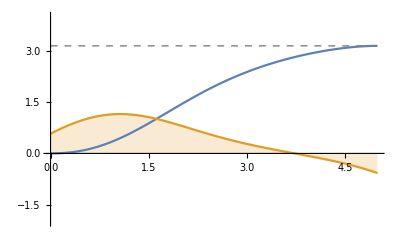

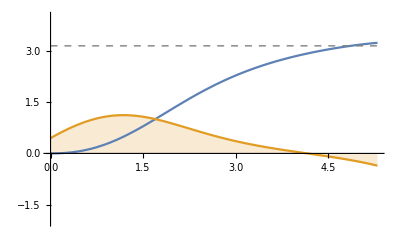

```mathematica
p1
p2
```

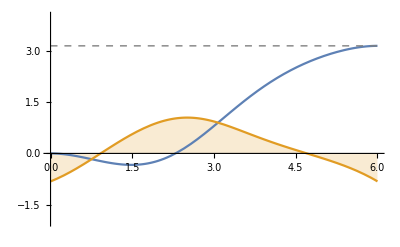

```mathematica
xsym = {θ,θdot,λ,λdot};nDim = 4; T = 5;n=200; dT = 0.0001;TFinal = 6;
{θ2,θdot2,u2,λ2,λdot2}=ffCalc[n,TFinal];
Plot[{θ2[t],u2[t],π},{t,0,TFinal},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-2,4}]
```